```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mean[θ_,σ_,n_]:=Pochhammer[θ + σ, n] / (σ Pochhammer[θ +1,n-1]) - θ / σ
```

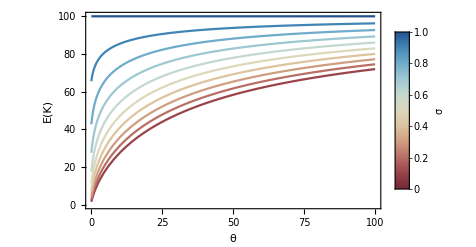

```mathematica
g=Legended[Show[Table[Plot[mean[θ, σ, 100],{θ,0, 100},PlotStyle->ColorData["RedBlueTones"][σ],PlotRange->{{0,100}, {0,100.1}},Frame->{True,True,False,False},FrameLabel->{"θ","E(K)"},LabelStyle->{Black,FontSize->16}],{σ,0.1,1,0.1}]],BarLegend["RedBlueTones",LegendLabel->"σ",LabelStyle->Directive[Black,FontSize->16]]]
```

```mathematica
Export["../figures/expectation_pochhammer.pdf", g]
```

../figures/expectation_pochhammer.pdf

```mathematica
PDF[PoissonDistribution[μ],i]
```

Piecewise[{{(ⅇ^-μ μ^i)/(i!), i≥0}, {0, True}}]

```mathematica
PDF[GammaDistribution[a,1/b],R]
```

Piecewise[{{((1/b)^-a ⅇ^(-b R) R^(-1+a))/Gamma[a], R>0}, {0, True}}]